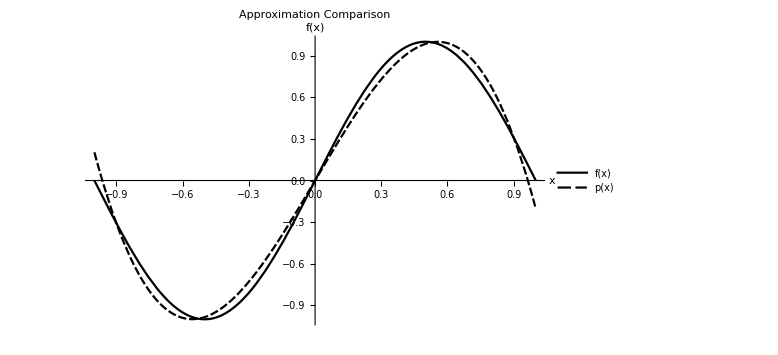

```mathematica
f[x_]=Sin[π x];
p[x_]=-(15(π^2-21))/(2 π^3)x+(35(π^2-15))/(2 π^3)x^3;
Plot[{f[x],p[x]},{x,-1,1},
PlotLabel->Style["Approximation Comparison",20],
PlotLegends->Placed[{"f(x)","p(x)"},{Bottom,Right}],
PlotTheme->"Monochrome",
AxesLabel->{"x","f(x)"},
ImageSize->Large]
```